```mathematica
ω[ω0_, α_, τ_, t_]:=Module[{
ans=((τ-t)^2 (2 ω0 t+τ (ω0+α t)))/τ^3*Boole[t ≤ τ]
},
ans/Max[1, Norm[ans]/5.5]
]
```

```mathematica
solveConstrained[θ0_, θ1_, ω0_, nsteps_, Δt_] := Module[{
α=-ω0,
τ = 1.0,
λ={0, 0, 0},
e=IdentityMatrix[3],
h=0.0001,
T=nsteps Δt,
αMax=6.5,
Δθ = AngleBetween[θ0, θTarget],
dfdα, d2fdα2, dgdα, H, G, A, b, Δ
},
α= RandomReal[{-3, 3}, 3];

(* Objective Function *)
Clear[f];
f[α_, τ_]:=Module[{ϕ = 0},
Do[
ϕ+=Norm[ω[ω0, α, τ, t]Δt],
{t, 0, T - Δt/2, Δt}
];
ϕ
];

(* Equality Constraints *)
Clear[g];
g[α_, τ_]:=Module[{θ=θ0},
Do[
θ=AxisAngleRotation[ω[ω0,α,τ,t]Δt].θ,
{t, 0, T - Δt/2, Δt}
];
AntisymmetricAxis[θ1.Transpose[θ]]
];

Do[
Print[{α, τ, f[α, τ], 180/π Norm[g[α, τ]]}];
dfdα=(f[α + h #, τ] - f[α, τ])/h& /@ e;
H = 1/h^2 Table[If[i == j,
-f[α-h e[[i]], τ] + 2f[α, τ]- f[α+h e[[i]], τ],
f[α+h e[[i]]+ h e[[j]], τ] - f[α-h e[[i]]+ h e[[j]], τ]  - f[α+h e[[i]]- h e[[j]], τ]  + f[α-h e[[i]]- h e[[j]], τ] 
], 
{i, 1, 3},
{j, 1, 3}
];
H = 1/2(H + Transpose[H]);
G=Transpose[(g[α + h #, τ] - g[α, τ])/h& /@ e];
A = ArrayFlatten[({{H, Transpose[G]}, {G, 0}})];
b = Join[dfdα + λ.G, g[α, τ]];
Δ = LinearSolve[A, b];
α -= Δ[[1;;3]];
λ -= Δ[[4;;6]];
If[Norm[α] > αMax,
τ *= Sqrt[Norm[α]/αMax];
α/=Norm[α]/αMax;
];
,
{k, 1,15}
];
Print[{α, τ, f[α, τ], 180/π Norm[g[α, τ]]}];
{α, τ}
]
```

```mathematica
ωTargetIterative[θ0_, θ1_, ω0_, nsteps_, Δt_] := Module[{
α = -ω0,
τ = 1.0,
eye = IdentityMatrix[3],
ϵ = 0.0001,
T = nsteps Δt,
αMax = 6.5,
r, J
},

r[α_, τ_]:=Module[{θ=θ0},
Do[
θ=AxisAngleRotation[ω[ω0, α, τ, t]Δt].θ;
,
{t,0,T-Δt/2,Δt}
];
AntisymmetricAxis[θ1.Transpose[θ]]
];

Do[
Print[{α, τ, r[α, τ]}];
J =Transpose[(r[α + ϵ #, τ] - r[α ,τ])/ϵ& /@ eye];
α -= LinearSolve[J, r[α, τ]];
If[Norm[α] > αMax,
τ *= Sqrt[Norm[α]/αMax];
α/=Norm[α]/αMax;
];
,
{k, 1,15}
];
Print[{α, τ, r[α, τ]}];
{α, τ}
]
```

```mathematica
ω0 = 4Normalize[RandomReal[{-1, 1}, 3]]
θ0 = RandomRotation[];
θTarget = RandomRotation[];
AngleBetween[θ0, θTarget]
```

{-0.1195,1.89399,-3.52116}

2.31261

```mathematica
AxisAngleRotation[{0, 3, 2}]
```

{{-0.894288,0.248224,-0.372336},{-0.248224,0.417142,0.874287},{0.372336,0.874287,-0.31143}}

```mathematica
nsteps = 60;
Δt = 1.0/60.0;
T = nsteps Δt;
```

{{-2.70576,-2.82399,-2.24119},1.,2.13359,60.0779}

{{6.11658,2.19883,-0.0506913},4.45159,4.84798,55.2481}

{{-4.6249,4.42078,1.14761},8.28324,5.01768,35.6124}

{{0.930758,5.51222,2.46319},8.28324,4.86787,27.0242}

{{-1.69769,4.2267,1.59831},8.28324,4.74842,8.26467}

{{-1.11455,4.25468,1.8602},8.28324,4.66885,0.601423}

{{-1.15453,4.22745,1.84764},8.28324,4.66464,0.00445753}

{{-1.15438,4.22732,1.84772},8.28324,4.66457,9.60285×10^-8}

{{-1.15438,4.22732,1.84772},8.28324,4.66457,4.79278×10^-13}

{{-1.15438,4.22732,1.84772},8.28324,4.66457,4.67444×10^-14}

{{-1.15438,4.22732,1.84772},8.28324,4.66457,3.25133×10^-14}

{{-1.15438,4.22732,1.84772},8.28324,4.66457,1.59821×10^-14}

{{-1.15438,4.22732,1.84772},8.28324,4.66457,4.49798×10^-15}

{{-1.15438,4.22732,1.84772},8.28324,4.66457,3.37349×10^-14}

{{-1.15438,4.22732,1.84772},8.28324,4.66457,3.07545×10^-14}

{{-1.15438,4.22732,1.84772},8.28324,4.66457,2.8845×10^-14}

{{-1.15438,4.22732,1.84772},8.28324}

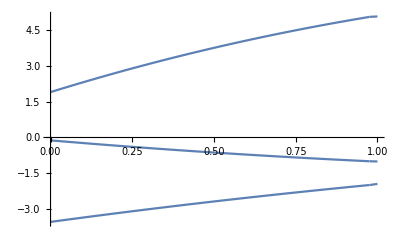

```mathematica
{α, τ} = solveConstrained[θ0, θTarget, ω0, nsteps, Δt]
Plot[ω[ω0, α, τ, t], {t,0,T}, PlotRange->All]
```

{{0.696581,-0.261156,0.668261},1.,{0.664604,-0.714641,-0.0141997}}

{{-4.43824,-2.0014,4.30656},3.41493,{0.195811,-0.664316,-0.546018}}

{{-1.75035,4.46933,4.38307},4.49518,{0.425151,-0.904731,-0.132241}}

{{-3.16681,-4.39156,3.59661},71.9693,{-0.538412,0.0972618,-0.645893}}

{{-2.69846,-2.09957,1.98932},71.9693,{0.206994,-0.509356,0.187605}}

{{-2.64749,-3.46169,2.42713},71.9693,{-0.056418,0.00409579,-0.19594}}

{{-2.83593,-3.20311,1.8964},71.9693,{-0.00515466,-0.00164468,-0.00452063}}

{{-2.83156,-3.20564,1.87446},71.9693,{-0.0000163097,2.03961×10^-7,-8.9193×10^-6}}

{{-2.83154,-3.20564,1.87442},71.9693,{-1.6292×10^-10,4.29567×10^-12,-6.51462×10^-11}}

{{-2.83154,-3.20564,1.87442},71.9693,{4.44089×10^-16,8.04912×10^-16,-1.66533×10^-16}}

{{-2.83154,-3.20564,1.87442},71.9693,{-4.996×10^-16,2.56739×10^-16,4.996×10^-16}}

{{-2.83154,-3.20564,1.87442},71.9693,{5.55112×10^-17,-5.13478×10^-16,-1.38778×10^-16}}

{{-2.83154,-3.20564,1.87442},71.9693,{2.22045×10^-16,3.33067×10^-16,-1.66533×10^-16}}

{{-2.83154,-3.20564,1.87442},71.9693,{-6.66134×10^-16,6.93889×10^-17,-5.55112×10^-17}}

{{-2.83154,-3.20564,1.87442},71.9693,{1.66533×10^-16,1.80411×10^-16,-1.11022×10^-16}}

{{-2.83154,-3.20564,1.87442},71.9693,{-1.11022×10^-16,1.45717×10^-16,3.33067×10^-16}}

{{-2.83154,-3.20564,1.87442},71.9693}

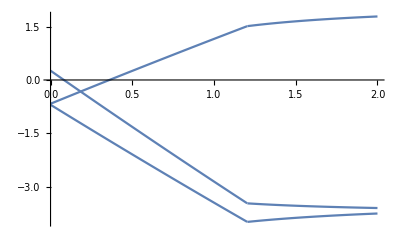

```mathematica
{α, τ} = ωTargetIterative[θ0, θTarget, ω0, nsteps, Δt]
Plot[ω[ω0, α, τ, t], {t,0,T}, PlotRange->All]
```

```mathematica
Evaluate[A]
```

{{1.×10^8 (-f$752031[{-3.64541,-3.29117,4.25793}]+2 f$752031[{-3.64531,-3.29117,4.25793}]-f$752031[{-3.64521,-3.29117,4.25793}]),4,-0.131825},4,{-0.131825,0.273957,-0.262175,0,0,0}}
 |  |  |  |

```mathematica
v = {0.05381349547852743,-1.6200039265549124,-0.8795123333426105,0.25};
α = v[[1;;3]];
τ = v[[4]];
```

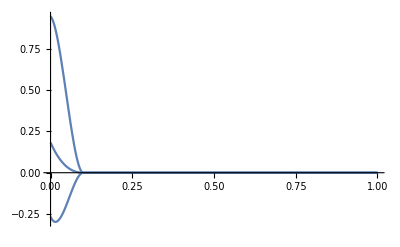

```mathematica
Plot[ω[ω0, α, τ, t], {t,0,T}, PlotRange->All]
```

```mathematica
NIntegrate[Norm[ω[ω0, α, τ, t]], {t, 0, T}]
```

1.22258

```mathematica
(* Objective Function *)
f2[{αx_, αy_, αz_,τ_}]:=Module[{ϕ = 0},
Do[
ϕ += Norm[ω[ω0, {αx, αy, αz}, τ, t]Δt],
{t, 0, T - Δt/2, Δt}
];
ϕ
];

(* Equality Constraints *)
g2[{αx_, αy_, αz_,τ_}]:=Module[{ϕ = 0,θ=θ0},
Do[
θ=AxisAngleRotation[ω[ω0, {αx, αy, αz}, τ, t]Δt].θ;
Print[AngleBetween[AxisAngleRotation[ω[ω0, {αx, αy, αz}, τ, t]Δt].θ, θ]];
,
{t, 0, T - Δt/2, Δt}
];
AntisymmetricAxis[θTarget.Transpose[θ]]
];
```

```mathematica
f2[Join[α, {τ}]]
```

7.94062

```mathematica
g2[Join[α, {τ}]]
```

0.0166667

0.0166845

0.0168025

0.0170183

0.017328

0.0177264

0.0182075

0.0187645

0.0193908

0.0200796

0.0208246

0.0216196

0.0224592

0.0233384

0.0242526

0.0251979

0.0261707

0.0271679

0.0281868

0.0292249

0.0302801

0.0313506

0.0324346

0.0335308

0.0346378

0.0357545

0.0368799

0.0380131

0.0391534

0.0403

0.0414523

0.0426096

0.0437716

0.0449378

0.0461076

0.0472809

0.0484572

0.0496362

0.0508176

0.0520013

0.0531869

0.0543742

0.0555632

0.0567535

0.057945

0.0591377

0.0603312

0.0615256

0.0627207

0.0639164

0.0651126

0.0663091

0.067506

0.0687031

0.0699004

0.0710978

0.0722951

0.0734925

0.0746898

0.0758869

0.0770838

0.0782805

0.0794769

0.080673

0.0818688

0.0830641

0.084259

0.0854535

0.0866474

0.0878409

0.0890337

0.0902261

0.0914178

0.0916667

0.0916667

0.0916667

«44 more identical outputs»

{-1.11022×10^-16,1.45717×10^-16,3.33067×10^-16}